```mathematica
Needs["ErrorBarPlots`"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data=Sort[Import["../data/iron/iron2commas.csv","CSV"],#1[[1]]<#2[[1]]&];
errorplotdata=Table[{{data[[i]][[1]],data[[i]][[3]]/data[[i]][[2]]},ErrorBar[Sqrt[data[[i]][[3]]]/data[[i]][[2]]]},{i,1,122}];
fitdata=Table[{data[[i]][[1]],data[[i]][[3]]/data[[i]][[2]]},{i,1,122}];
weightdata=Table[1/(Sqrt[data[[i]][[3]]]/data[[i]][[2]])^2,{i,1,122}];
```

```mathematica
Length[data]
```

122

```mathematica
lorentz[x_,A_,B_,γ_,x0_]:=A-B/(π*γ)*1/(1+((x-x0)/γ)^2);
lorentzall[x_,B_,γ_,x0_]:=-B/(π*γ)*1/(1+((x-x0)/γ)^2);
```

```mathematica
allpeaks=NonlinearModelFit[fitdata,A+lorentzall[x,B1,γ1,x01]+lorentzall[x,B2,γ2,x02]+lorentzall[x,B3,γ3,x03]+lorentzall[x,B4,γ4,x04]+lorentzall[x,B5,γ5,x05]+lorentzall[x,B6,γ6,x06],{{A,0.048},B1,B2,B3,B4,B5,B6,γ1,γ2,γ3,γ4,γ5,γ6,{x01,-5.3},{x02,-3},{x03,-0.7},{x04,0.8},{x05,3},{x06,5.3}},x,Weights->weightdata]
```

FittedModel[«1»]

```mathematica
fitpeak1=NonlinearModelFit[fitdata[[1;;20]],lorentz[x,A,B,γ,x0],{A,B,γ,{x0,-5.3}},x,Weights->weightdata[[1;;20]]]
fitpeak2=NonlinearModelFit[fitdata[[24;;40]],lorentz[x,A,B,γ,x0],{A,B,γ,{x0,-3}},x,Weights->weightdata[[24;;40]]]
fitpeak3=NonlinearModelFit[fitdata[[48;;62]],lorentz[x,A,B,γ,x0],{A,B,γ,{x0,-0.7}},x,Weights->weightdata[[48;;62]]]
fitpeak4=NonlinearModelFit[fitdata[[62;;78]],lorentz[x,A,B,γ,x0],{A,B,γ,{x0,0.8}},x,Weights->weightdata[[62;;78]]]
fitpeak5=NonlinearModelFit[fitdata[[84;;104]],lorentz[x,A,B,γ,x0],{A,B,γ,{x0,3}},x,Weights->weightdata[[84;;104]]]
fitpeak6=NonlinearModelFit[fitdata[[104;;122]],lorentz[x,A,B,γ,x0],{A,B,γ,{x0,5.3}},x,Weights->weightdata[[104;;122]]]
```

FittedModel[0.048636-0.0036589/(1+«19» ((«1»«1»)^2)]

FittedModel[0.0465325-0.00219248/(1+«19» («1»)^2)]

FittedModel[0.0464458-0.00180612/(1+«19» («1»)^2)]

FittedModel[0.0465769-0.00177835/(1+«19» ((«1»«1»)^2)]

FittedModel[0.0470134-0.00247214/(1+«19» («1»)^2)]

FittedModel[0.0469617-0.00278837/(1+«19» ((«1»«1»)^2)]

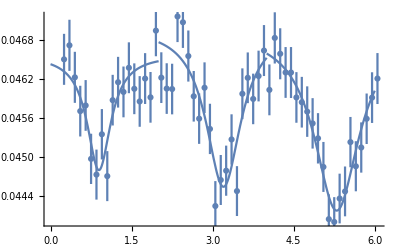

```mathematica
Show[ErrorListPlot[errorplotdata[[64;;122]]],Plot[Normal[fitpeak4],{x,0,2}],Plot[Normal[fitpeak5],{x,2,4}],Plot[Normal[fitpeak6],{x,4,6}]]
```

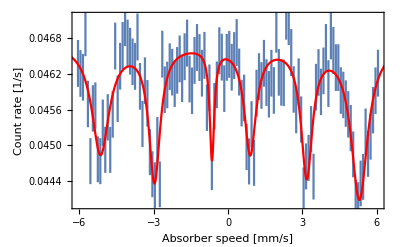

```mathematica
Show[ErrorListPlot[errorplotdata,PlotStyle->{PointSize->0},Frame->True],Plot[Normal[allpeaks],{x,-7,7},PlotStyle->Red],ImageSize->Full,FrameStyle->{Thick,Black},LabelStyle->{FontSize->18,Bold,Black},FrameLabel->{"Absorber speed [mm/s]","Count rate [1/s]"}]
```

```mathematica
Sum[allpeaks["FitResiduals"][[i]]^2*weightdata[[i]],{i,1,Length[allpeaks["FitResiduals"]]}]/(Length[allpeaks["FitResiduals"]]-Length[allpeaks["ParameterTable"][[1]][[1]]-1])
```

1.0268

```mathematica
allpeaks["ParameterTable"][[1]][[1]]
```

{{,Estimate,Standard Error,t-Statistic,P-Value},{A,0.0467239,0.000120314,388.351,7.08475×10^-165},{B1,0.00248005,0.000489474,5.06676,1.78601×10^-6},{B2,0.00198434,0.000356498,5.56619,2.07853×10^-7},{B3,0.000647999,0.000178915,3.62181,0.000455922},{B4,0.00163881,0.000368995,4.44128,0.000022545},{B5,0.00188774,0.000343354,5.49796,2.80526×10^-7},{B6,0.00331007,0.000466436,7.09652,1.67898×10^-10},{γ1,0.429056,0.0903817,4.74715,6.68114×10^-6},{γ2,0.277993,0.0565765,4.91357,3.38133×10^-6},{γ3,0.111732,0.0356259,3.13626,0.00223081},{γ4,0.287921,0.0728352,3.95304,0.000141711},{γ5,0.277595,0.0579225,4.79253,5.55607×10^-6},{γ6,0.406843,0.0620644,6.55518,2.24949×10^-9},{x01,-5.14125,0.050316,-102.179,2.36424×10^-105},{x02,-2.96434,0.0325288,-91.1296,2.73894×10^-100},{x03,-0.645721,0.0283758,-22.756,5.69947×10^-42},{x04,0.896031,0.0416046,21.5368,6.24013×10^-40},{x05,3.17592,0.0340916,93.1584,2.91309×10^-101},{x06,5.29991,0.0347694,152.43,3.99313×10^-123}}

```mathematica
x0data=Table[{allpeaks["ParameterTable"][[1]][[1]][[i]][[2]],allpeaks["ParameterTable"][[1]][[1]][[i]][[3]]},{i,15,20}]
```

{{-5.14125,0.050316},{-2.96434,0.0325288},{-0.645721,0.0283758},{0.896031,0.0416046},{3.17592,0.0340916},{5.29991,0.0347694}}

```mathematica
c=2.998*10^8;
```

```mathematica
delEdata=x0data/c/1000*14400*10^(9)
```

{{-246.945,2.41678},{-142.383,1.56243},{-31.0153,1.36295},{43.0382,1.99835},{152.546,1.63749},{254.565,1.67005}}

```mathematica
viso16=(x0data[[6]][[1]]+x0data[[1]][[1]])/2
sviso16=Sqrt[(x0data[[6]][[2]]^2+x0data[[1]][[2]]^2)]/2
viso25=(x0data[[5]][[1]]+x0data[[2]][[1]])/2
sviso25=Sqrt[(x0data[[5]][[2]]^2+x0data[[2]][[2]]^2)]/2
viso34=(x0data[[4]][[1]]+x0data[[3]][[1]])/2
sviso34=Sqrt[(x0data[[4]][[2]]^2+x0data[[3]][[2]]^2)]/2
```

0.0793275

0.0305803

0.105788

0.0235603

0.125155

0.02518

```mathematica
mviso=WeightedData[{viso16,viso25,viso34},{sviso16,sviso25,sviso34}];
```

```mathematica
Mean[mviso]
StandardDeviation[mviso]
```

0.101735

0.0237165

```mathematica
Eiso16=(delEdata[[6]][[1]]+delEdata[[1]][[1]])/2
sEiso16=Sqrt[(delEdata[[6]][[2]]^2+delEdata[[1]][[2]]^2)]/2
Eiso25=(delEdata[[5]][[1]]+delEdata[[2]][[1]])/2
sEiso25=Sqrt[(delEdata[[5]][[2]]^2+delEdata[[2]][[2]]^2)]/2
Eiso34=(delEdata[[4]][[1]]+delEdata[[3]][[1]])/2
sEiso34=Sqrt[(delEdata[[4]][[2]]^2+delEdata[[3]][[2]]^2)]/2
```

3.81026

1.46883

5.0812

1.13165

6.01144

1.20945

```mathematica
mEiso=WeightedData[{Eiso16,Eiso25,Eiso34},{sEiso16,sEiso25,sEiso34}];
```

```mathematica
Mean[mEiso]
StandardDeviation[mEiso]
```

4.88652

1.13915

```mathematica
muea={0.146,0.005};
mueb={0.162,0.003};
muec={0.160,0.003};
mug={0.09044,0.0007};
muN=3.152*10^(-20);
delva=
```